## A reanalysis of the SH0ES data for H_0. The histograms of distributions of the period and metallicity in the Cepheids sample - Kolmogorov Smirnov Test

## Setting the directory

```mathematica
SetDirectory[NotebookDirectory[]];
Needs["ErrorBarPlots`"];
Needs["ErrorBarLogPlots`"]
Off[General::"obspkg",General::luc,NIntegrate::"inumr",NIntegrate::ncvb,CompiledFunction::cflist,ListInterpolation::inhr,FindMinimum::lstol];
```

## Data-Period-Figure 6

```mathematica
dataperiod=Import[".\\data\\logp.txt","Table"];
```

```mathematica
sampleP[dataperiod_]:=Table[dataperiod[[i,1]]+1,{i,1,3130}]
```

```mathematica
sp=sampleP[dataperiod];
```

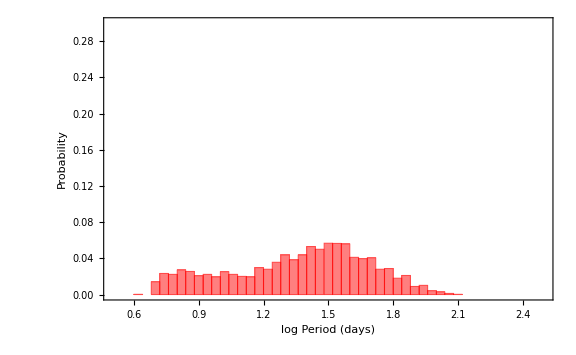

```mathematica
hisp=Histogram[{sp},{0.04},"Probability",ChartLabels->"logP",BaseStyle->FontSize->20,PlotRange->{{0.5,2.5},{0,0.3}},FrameLabel->{"log Period (days)","Probability"},Frame->True,Axes->None,ChartStyle->Red,FrameStyle->Directive[Black,Thick],ImageSize->Large]
```

```mathematica
N0105P[dataperiod_]:=Table[dataperiod[[i,1]]+1,{i,321,328}]
```

```mathematica
N0105P[dataperiod]
```

{1.49208,1.51003,1.5612,1.5667,1.56699,1.60546,1.74602,1.79364}

```mathematica
N0976P[dataperiod_]:=Table[dataperiod[[i,1]]+1,{i,2085,2117}]
```

```mathematica
N0976P[dataperiod]
```

{1.47647,1.69769,1.57817,1.53561,1.7085,1.57008,1.56346,1.62098,1.59836,1.57646,1.51075,1.63137,1.59165,1.55562,1.56357,1.48562,1.58688,1.77859,1.62317,1.70041,1.61518,1.48948,1.71504,1.63507,1.70804,1.60643,1.49366,1.66258,1.48147,1.70605,1.6422,1.47405,1.48815}

```mathematica
sp1=Join[N0105P[dataperiod],N0976P[dataperiod]]
```

{1.49208,1.51003,1.5612,1.5667,1.56699,1.60546,1.74602,1.79364,1.47647,1.69769,1.57817,1.53561,1.7085,1.57008,1.56346,1.62098,1.59836,1.57646,1.51075,1.63137,1.59165,1.55562,1.56357,1.48562,1.58688,1.77859,1.62317,1.70041,1.61518,1.48948,1.71504,1.63507,1.70804,1.60643,1.49366,1.66258,1.48147,1.70605,1.6422,1.47405,1.48815}

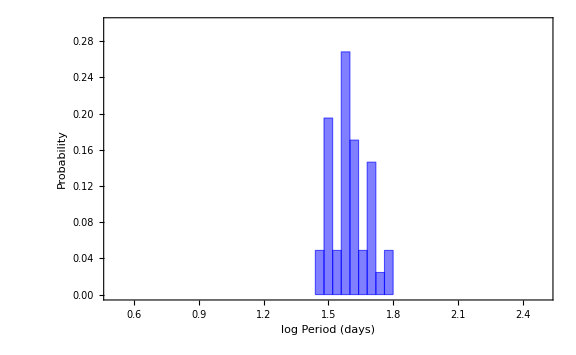

```mathematica
hisp1=Histogram[{sp1},{0.04},"Probability",ChartLabels->"logP",BaseStyle->FontSize->20,PlotRange->{{0.5,2.5},{0,0.3}},FrameLabel->{"log Period (days)","Probability"},Frame->True,Axes->None,ChartStyle->{Blue,Opacity[0.1]},FrameStyle->Directive[Black,Thick],ImageSize->Large]
```

```mathematica
sp2=Drop[Drop[sp,{2085,2117}],{321,328}];
```

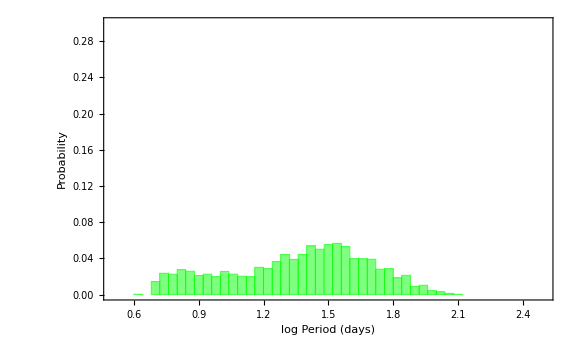

```mathematica
hisp2=Histogram[{sp2},{0.04},"Probability",ChartLabels->"logP",BaseStyle->FontSize->20,PlotRange->{{0.5,2.5},{0,0.3}},FrameLabel->{"log Period (days)","Probability"},Frame->True,Axes->None,ChartStyle->{Green,Opacity[0.1]},FrameStyle->Directive[Black,Thick],ImageSize->Large]
```

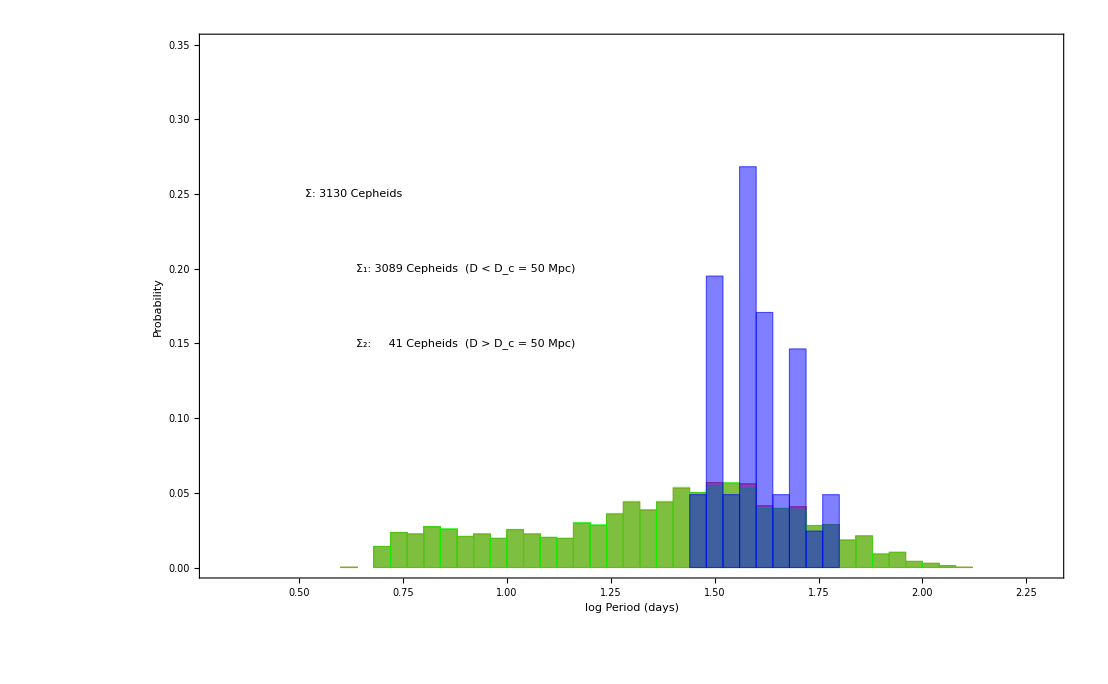

```mathematica
fighisp=Show[hisp,hisp2,hisp1,Graphics[{Inset["Σ: 3130 Cepheids  " ,{0.63 ,0.25},BaseStyle->{Italic,Red,FontFamily->"Times",16}]}],Graphics[{Inset["Σ_1: 3089 Cepheids  (D < D_c = 50 Mpc)" ,{0.9,0.2},BaseStyle->{Italic,Green,FontFamily->"Times",16}]}],Graphics[{Inset["Σ_2:     41 Cepheids  (D > D_c = 50 Mpc)" ,{0.9,0.15},BaseStyle->{Italic,Blue,FontFamily->"Times",16}]}],BaseStyle->18,FrameLabel->{"log Period (days)","Probability"},PlotRange->{{0.3,2.3},{0,0.35}},LabelStyle->{FontFamily->"Times",20},Axes->None,FrameStyle->Directive[Black],Frame->True,ImageSize->Large]
```

```mathematica
Export[NotebookDirectory[]<>"fighisp.pdf",fighisp,ImageResolution->1000];
```

## Data-Metallicity-Figure 7

```mathematica
ldata=Import[".\\data\\alll_shoes_ceph_topantheonwt6.0_112221.fits","RawData"]//Normal;
```

```mathematica
trL=ldata[[1]]
```

{1}
 |  |  |  |

```mathematica
L=Transpose[trL];
```

```mathematica
colmet=L[[All,44]];
```

```mathematica
sampleM[colmet_]:=Table[colmet[[i]],{i,1,3130}]
```

```mathematica
sm=sampleM[colmet];
```

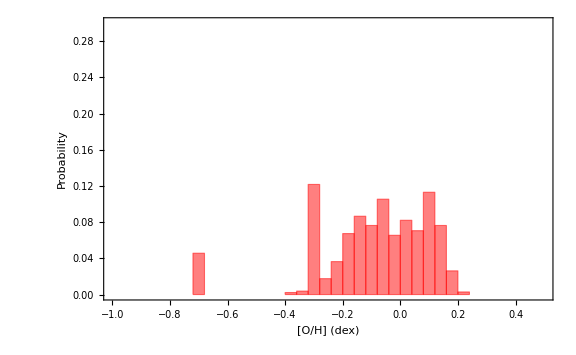

```mathematica
hism=Histogram[{sm},{0.04},"Probability",ChartLabels->"[O/H] (dex)",BaseStyle->FontSize->20,PlotRange->{{-1,0.5},{0,0.3}},FrameLabel->{"[O/H] (dex)","Probability"},Frame->True,Axes->None,ChartStyle->Red,FrameStyle->Directive[Black,Thick],ImageSize->Large]
```

```mathematica
N0105M[sm_]:=Table[sm[[i]],{i,321,328}]
```

```mathematica
N0105M[sm]
```

{-0.17947,-0.17817,-0.0674596,-0.10013,-0.0511796,-0.15116,-0.1359,-0.16579}

```mathematica
N0976M[sm_]:=Table[sm[[i]],{i,2085,2117}]
```

```mathematica
N0976M[sm]
```

{0.0175504,0.0244104,-0.0241296,-0.00221958,0.0421004,0.0440204,0.0399504,0.0314704,-0.0413696,0.0325304,-0.00231958,0.0568204,0.0711004,0.0431204,0.00101042,-0.0330096,-0.0795096,0.0838604,0.0254204,0.0641104,0.0590304,0.0541104,0.0594404,0.0190004,0.0217304,0.0402504,0.0169804,-0.0124396,0.00382042,0.0682504,0.0228204,0.0305704,0.0465004}

```mathematica
sm1=Join[N0105M[sm],N0976M[sm]]
```

{-0.17947,-0.17817,-0.0674596,-0.10013,-0.0511796,-0.15116,-0.1359,-0.16579,0.0175504,0.0244104,-0.0241296,-0.00221958,0.0421004,0.0440204,0.0399504,0.0314704,-0.0413696,0.0325304,-0.00231958,0.0568204,0.0711004,0.0431204,0.00101042,-0.0330096,-0.0795096,0.0838604,0.0254204,0.0641104,0.0590304,0.0541104,0.0594404,0.0190004,0.0217304,0.0402504,0.0169804,-0.0124396,0.00382042,0.0682504,0.0228204,0.0305704,0.0465004}

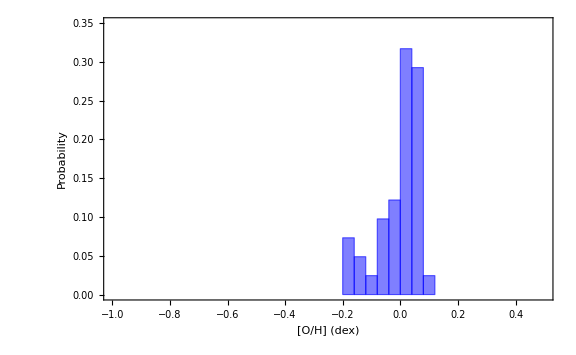

```mathematica
hism1=Histogram[{sm1},{0.04},"Probability",ChartLabels->"[O/H] (dex)",BaseStyle->FontSize->20,PlotRange->{{-1,0.5},{0,0.35}},FrameLabel->{"[O/H] (dex)","Probability"},Frame->True,Axes->None,ChartStyle->{Blue,Opacity[0.1]},FrameStyle->Directive[Black,Thick],ImageSize->Large]
```

```mathematica
sm2=Drop[Drop[sm,{2085,2117}],{321,328}];
```

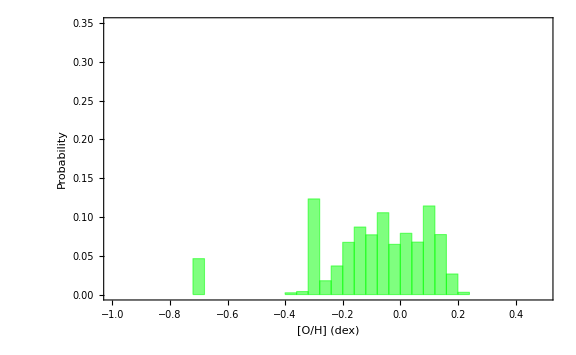

```mathematica
hism2=Histogram[{sm2},{0.04},"Probability",ChartLabels->"[O/H] (dex)",BaseStyle->FontSize->20,PlotRange->{{-1,0.5},{0,0.35}},FrameLabel->{"[O/H] (dex)","Probability"},Frame->True,Axes->None,ChartStyle->{Green,Opacity[0.1]},FrameStyle->Directive[Black,Thick],ImageSize->Large]
```

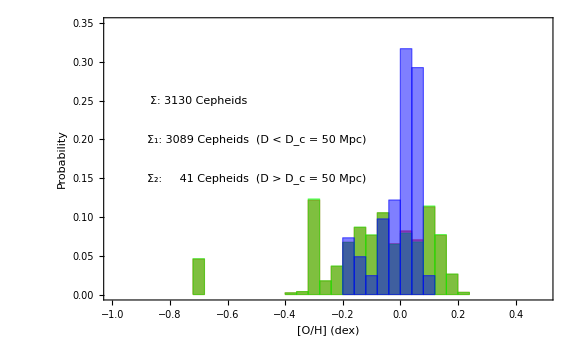

```mathematica
fighism=Show[hism,hism2,hism1,Graphics[{Inset["Σ: 3130 Cepheids " ,{-0.7,0.25},BaseStyle->{Italic,Red,FontFamily->"Times",16}]}],Graphics[{Inset["Σ_1: 3089 Cepheids  (D < D_c = 50 Mpc)" ,{-0.5,0.2},BaseStyle->{Italic,Green,FontFamily->"Times",16}]}],Graphics[{Inset["Σ_2:     41 Cepheids  (D > D_c = 50 Mpc)" ,{-0.5,0.15},BaseStyle->{Italic,Blue,FontFamily->"Times",16}]}],BaseStyle->18,FrameLabel->{"[O/H] (dex)","Probability"},PlotRange->{{-1,0.5},{0,0.35}},LabelStyle->{FontFamily->"Times",20},Axes->None,FrameStyle->Directive[Black],Frame->True,ImageSize->Large]
```

```mathematica
Export[NotebookDirectory[]<>"fighism.pdf",fighism,ImageResolution->1000];
```

## Kolmogorov-Smirnov Test

```mathematica
n=Length[sp1];
m=Length[sp2];
r1=RandomChoice[sp1,n];
```

```mathematica
r2=RandomChoice[sp2,m];
```

```mathematica
k=Length[sm1];
l=Length[sm2];
s1=RandomChoice[sm1,n];
```

```mathematica
s2=RandomChoice[sm2,m];
```

```mathematica
KolmogorovSmirnovTest[r1,r2,"TestDataTable"]
```

| Statistic | P-Value
Kolmogorov-Smirnov | 0.575915 | 4.40559×10^-12

```mathematica
KolmogorovSmirnovTest[s1,s2,"TestDataTable"]
```

| Statistic | P-Value
Kolmogorov-Smirnov | 0.334499 | 0.000233663

```mathematica
KolmogorovSmirnovTest[r1,r2,"TestConclusion"]
```

The null hypothesis that the datasets have the same distribution is rejected at the 5 percent level based on the Kolmogorov-Smirnov test.

```mathematica
KolmogorovSmirnovTest[s1,s2,"TestConclusion"]
```

The null hypothesis that the datasets have the same distribution is rejected at the 5 percent level based on the Kolmogorov-Smirnov test.

```mathematica
KolmogorovSmirnovTest[r1,r2,"ShortTestConclusion"]
```

Reject

```mathematica
KolmogorovSmirnovTest[s1,s2,"ShortTestConclusion"]
```

Reject